3/5

(0 | 0.321513
3/5 | 0.564545
6/5 | 1.05291
9/5 | 1.87865
12/5 | 2.40318
3 | 2.10102
18/5 | 1.43302
21/5 | 0.810583
24/5 | 0.382893
27/5 | 0.151072
6 | 0.0497871)

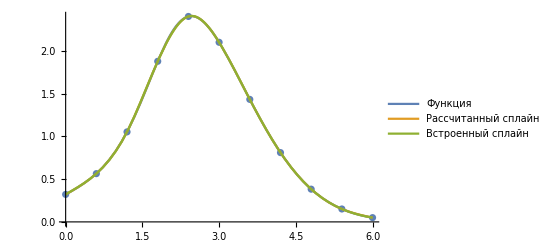

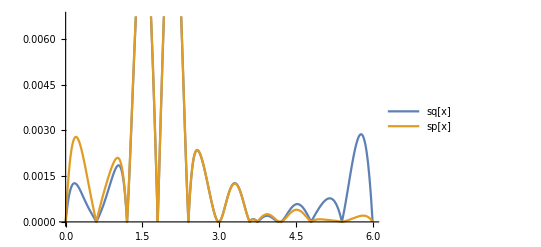

{0.00901106,{x→1.26682}}

```mathematica
a = 0;b=6;n =10; (*Изначальные параметры*)
 h=(b-a)/n (*Расчет шага*)
f[x_]:=(Exp[x-x^2/4]*Tanh[x^3/11+1/3]);(*Заданная функция*)
Array[xdata,n+1,0];Array[ydata,n+1,0];
Array[d,n,0];Array[w,n,0];Array[{p,q,r,o},n,1];
For[i=0,i<=n,i++,(*Расчет значений x и y, согласно заданной функции*)
xdata[i] = a+i×h;
ydata[i]=N[f[xdata[i]]];
];
For[i=0,i<=n,i++,  (*Метод прогонки для расчета коэффициентов сплайна*)
d[i]=xdata[i+1]-xdata[i];
w[i]=ydata[i+1]-ydata[i]];
p[1]=0;r[n]=0;
For[i=1,i<=n,i++,
p[i]=d[i-1];
r[i]=d[i];
q[i]=2*(d[i]+d[i-1]);
o[i]=3*(w[i]/d[i]-w[i-1]/d[i-1])];
Array[u,n,1];Array[v,n,1];Array[cs,n,0];
u[1]=-r[1]/q[1];
v[1]=o[1]/q[1];
For[i=2,i<n,i++,
s=q[i]+p[i]*u[i-1];
u[i]=-r[i]/s;
v[i]=(o[i]-p[i]*v[i-1])/s];
cs[0]=0;
cs[n]=0;
For[i=n-1,i>=1,i--,
cs[i]=u[i]*cs[i+1]+v[i]];
spln[xdata_,ydata_,cs_,n_,x_]:=Block[{i=0,h1,a1,b1,c1,d1,t1},While[x>xdata[i+1],i++];(*Расчет коэффициентов рассчитанного сплайна*)
h1=xdata[i+1]-xdata[i];
a1=ydata[i];
b1=(ydata[i+1]-ydata[i])/h1-(cs[i+1]+2*cs[i])*h1/3;
c1=cs[i];
d1=(cs[i+1]-cs[i])/(3*h1);
t1=x-xdata[i];
Return[a1+b1*t1+c1*t1*t1+d1*t1*t1*t1]];
sq[x_]:=spln[xdata,ydata,cs,n,x](*функция-ссылка на рассчитанный сплайн spln*)
data1=Table[{xdata[i],N[ydata[i]]},{i,0,n}];
MatrixForm[data1]
sp=Interpolation[data1,Method->"Spline"];(*Объявление встроеннного сплайна*)
gr1:=ListPlot[data1];
gr2:=Plot[{f[x],sq[x],sp[x]},{x,xdata[0],xdata[n]},PlotLegends->{"Функция","Рассчитанный сплайн","Встроенный сплайн"}]
Show[{gr1,gr2}](*Вывод графиков встроенного и рассчитанного сплайнов, а также самой функции f(x)*)
errSq[x_]:=Abs[sq[x]-f[x]];
errSp[x_]:=Abs[sp[x]-f[x]]
gr3:=Plot[{errSq[x],errSp[x]},{x,a,b},PlotLegends->{"sq[x]","sp[x]"}]
Show[gr3](*Вывод графика погрешностей*)
FindMaximum[{errSq[x],a<=x<=b},x]
```